# Palomar 5

## Chapel

#### Version 0 Backwards Integration of Palomar 5 (works) N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 4000000 Msun

Import Coordinates

```mathematica
chxcl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test.csv",{"Data",2;;6001,1}];
chycl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test.csv",{"Data",2;;6001,2}];
chxclv =  Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test.csv",{"Data",2;;6001,3}];
chyclv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test.csv",{"Data",2;;6001,4}];
```

Transpose Coordinates

```mathematica
chcl = Transpose[{chxcl,chycl}];
chclv = Transpose[{chxclv,chyclv}];
```

#### Version 1 Full integration of Palomar 5 N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 4000000 Msun Prints snapshot at 6000th timestep

Import Coordinates

```mathematica
ch1cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test1.csv",{"Data",2,1;;2}];
ch1clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test1.csv",{"Data",2,3;;4}];
ch1lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test1.csv",{"Data",3;;6001,1;;2}];
ch1tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test1.csv",{"Data",3;;6001,5;;6}];
```

#### Version 2 Full integration of Palomar 5 N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 4000000 Msun Prints snapshot at 5000th timestep

Import Coordinates

```mathematica
ch2cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test2.csv",{"Data",5002,1;;2}];
ch2clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test2.csv",{"Data",5002,3;;4}];
ch2lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test2.csv",{"Data",2;;5001,1;;2}]
ch2tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test2.csv",{"Data",2;;5001,5;;6}];
```

{{8.96546×10^9,-5.3429×10^7},{8.96546×10^9,-5.34292×10^7},{8.96546×10^9,-5.34294×10^7},{8.96547×10^9,-5.34295×10^7},4992,{8.9683×10^9,-5.37371×10^7},{8.9683×10^9,-5.37371×10^7},{8.9683×10^9,-5.37371×10^7},{8.9683×10^9,-5.37371×10^7}}
 |  |  |  |

#### Version 3 Backward and Forward Integration of Cluster (kpc) N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1000000000 Msun

Import Coordinates

```mathematica
ch3clback = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test3.csv",{"Data",2;;6002,1;;2}];
ch3clvback = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test3.csv",{"Data",2;;6002,3;;4}];
ch3clfwd = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test3.csv",{"Data",6003;;12002,1;;2}];
ch3clvfwd = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test3.csv",{"Data",6003;;12002,3;;4}];
```

#### Version 4: Initial positions of ejected stars (kpc) N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 4000000 Msun

Import Coordinates

```mathematica
ch4cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test4.csv",{"Data",6001,1;;2}];
ch4lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test4.csv",{"Data",2;;6000,1;;2}];
ch4tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test4.csv",{"Data",2;;6000,5;;6}];
```

#### Version 5: snapshot at 6000th timestep (kpc) N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1,000,000,000 Msun

Import Coordinates

```mathematica
ch5cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test5.csv",{"Data",2,1;;2}]
ch5clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test5.csv",{"Data",2,3;;4}];
ch5lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test5.csv",{"Data",3;;6001,1;;2}];
ch5tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test5.csv",{"Data",3;;6001,5;;6}];
```

{50.0086,9.37126×10^-15}

### Version 6 (NFW potential) (kpc)

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity * years/Myr Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1,000,000,000 Msun

```mathematica
ch6cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test6.csv",{"Data",2,1;;2}];
ch6clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test6.csv",{"Data",2,3;;4}];
ch6lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test6.csv",{"Data",3;;6001,1;;2}];
ch6tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/test6.csv",{"Data",3;;6001,5;;6}];
```

## C

### Version 0: Backwards Integration of Palomar 5

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 4000000 Msun

### Version 1 Full integration of Palomar 5 (kpc)

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1,000,000,000 Msun Prints snapshot at 6000th timestep

Import Coordinates

```mathematica
c1cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest1.csv",{"Data",2,1;;2}];
c1clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest1.csv",{"Data",2,3;;4}];
c1lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest1.csv",{"Data",3;;6001,1;;2}];
c1tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest1.csv",{"Data",3;;6001,5;;6}];
```

### Version 2 NFW galactic potential (kpc)

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1,000,000,000 Msun Prints snapshot at 6000th timestep

```mathematica
c2cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest2.csv",{"Data",2,1;;2}];
c2clv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest2.csv",{"Data",2,3;;4}];
c2lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest2.csv",{"Data",3;;6001,1;;2}];
c2tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest2.csv",{"Data",3;;6001,5;;6}];
```

### Version 3 Initial positions of ejected stars (kpc)

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1,000,000,000 Msun

```mathematica
c3cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest3.csv",{"Data",6001,1;;2}];
c3lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest3.csv",{"Data",2;;6000,1;;2}];
c3tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest3.csv",{"Data",2;;6000,5;;6}];
```

### Version 4 backward and forward integration of cluster (kpc)

#### N = 6000, dt = 1,000,000 years, M = 1 Mass of Cluster = 20,000 Msun (no mass loss) Initial Position of Cluster = 50 kpc,0,0 Initial Velocity of Cluster = 0.5 * centripetal velocity Rcl = 20 pc = 4.126 * 10^6 AU central potential = 1000000000 Msun

```mathematica
c4clback = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest4.csv",{"Data",2;;6002,1;;2}];
c4clvback = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest4.csv",{"Data",2;;6002,3;;4}];
c4clfwd = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest4.csv",{"Data",6003;;12002,1;;2}];
c4clvfwd = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/ctest4.csv",{"Data",6003;;12002,3;;4}];
```

## Graphs

#### chpl version 0 (backward)

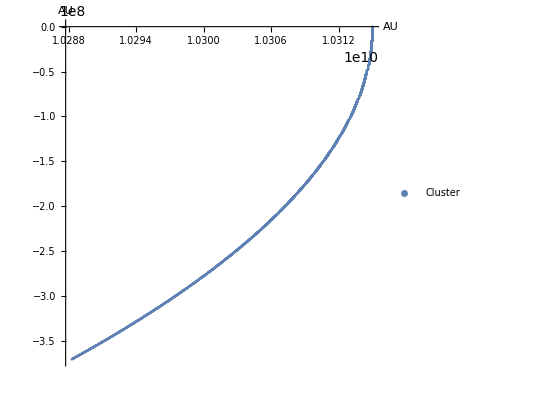

```mathematica
chorbit = ListPlot[{chcl},ImageSize->Full,AxesLabel->{"AU","AU"},AspectRatio ->1, PlotLegends->{"Cluster"}]
```

#### chpl version 1 (full, 6000th timestep)

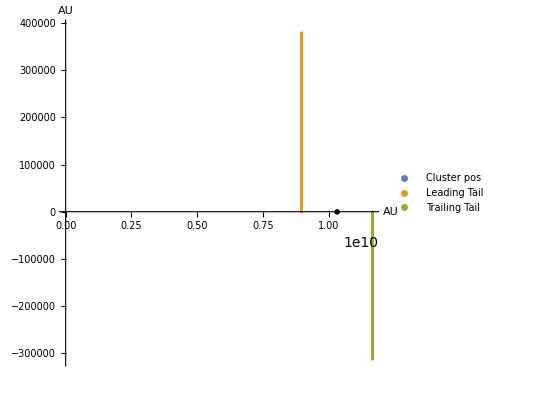

```mathematica
ch1orbit = ListPlot[{ch1cl,ch1lt,ch1tt},ImageSize->Full,AxesLabel->{"AU","AU"},AspectRatio ->1, PlotLegends->{"Cluster pos","Leading Tail","Trailing Tail"},Epilog -> {PointSize[0.01], Point[{ch1cl}],PlotLegends->{"Cluster pos"}}]
```

#### chpl version 2 (full, 5000th timestep)

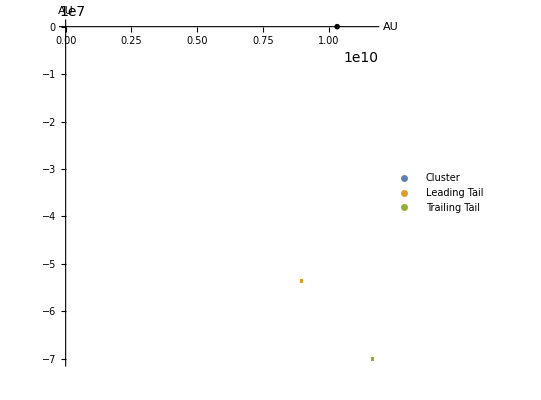

```mathematica
ch2orbit = ListPlot[{ch2cl, ch2lt,ch2tt},ImageSize->Full,AxesLabel->{"AU","AU"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch2cl}]}, PlotLegends->{"Cluster","Leading Tail","Trailing Tail"}]
```

#### chpl version 3 (backward and forward)

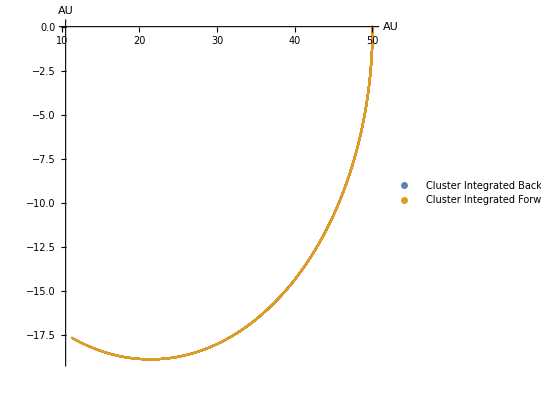

```mathematica
ch3orbit = ListPlot[{ch3clback,ch3clfwd},ImageSize->Full,AxesLabel->{"AU","AU"},AspectRatio ->1, PlotLegends->{"Cluster Integrated Backwards","Cluster Integrated Forwards"}]
```

#### chpl version 4 (initial positions of ejected particles)

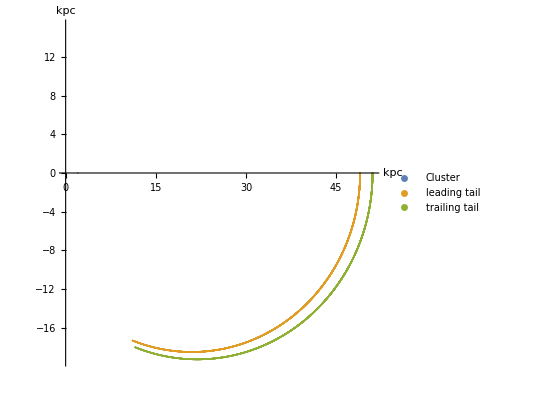

```mathematica
ch4orbit = ListPlot[{ch4cl,ch4lt,ch4tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, PlotLegends->{"Cluster","leading tail","trailing tail"}]
```

#### c version 1 (full, 6000th timestep)

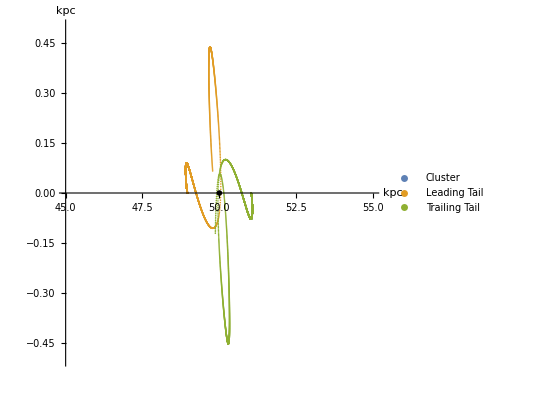

```mathematica
c1orbit = ListPlot[{c1cl,c1lt,c1tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, PlotLegends-> {"Cluster","Leading Tail","Trailing Tail"},Epilog -> {PointSize[0.01], Point[{c1cl}]},PlotRange->{{45,55},{-0.5,0.5}}]
```

#### chpl version 5 (6000th timestep, diff)

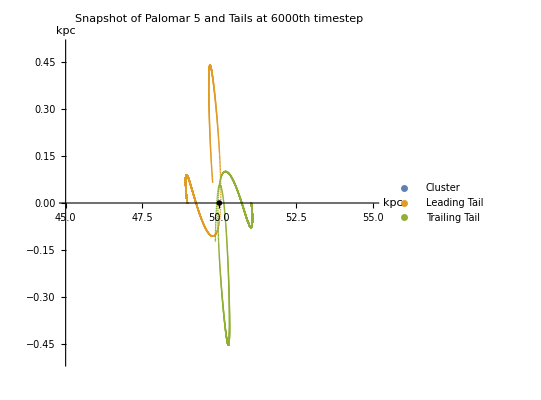

```mathematica
ch5orbit = ListPlot[{ch5cl,ch5lt,ch5tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch5cl}]}, PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold, PlotRange->{{45,55},{-0.5,0.5}}]
```

#### chpl version 6 (NFW galactic potential)

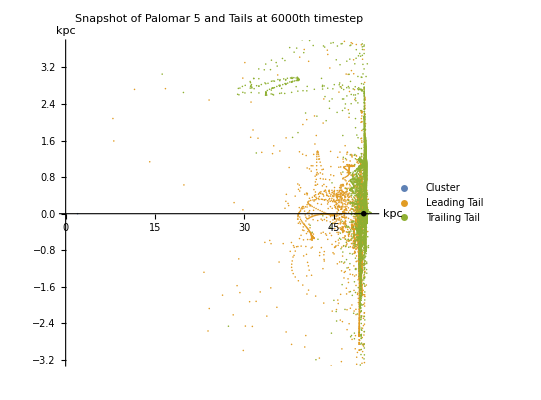

```mathematica
ch6orbit = ListPlot[{ch6cl,ch6lt,ch6tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{ch5cl}]}, PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange-> Automatic, PlotLabel->Style[Framed["Snapshot of Palomar 5 and Tails at 6000th timestep"],FontSize->18],LabelStyle->Bold]
```

#### c version 2 (NFW galactic potential)

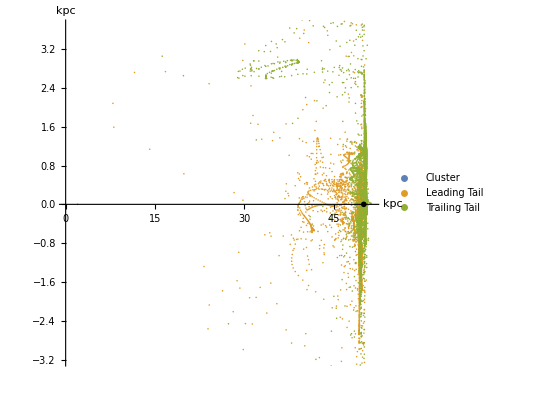

```mathematica
c2orbit = ListPlot[{c2cl,c2lt,c2tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{c2cl}]}, PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange-> Automatic]
```

#### c version 3 (initial positions of ejected stars)

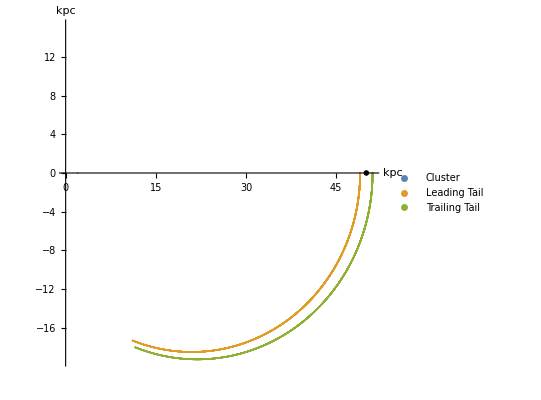

```mathematica
c3orbit = ListPlot[{c3cl,c3lt,c3tt},ImageSize->Full,AxesLabel->{"kpc","kpc"},AspectRatio ->1, Epilog -> {PointSize[0.01], Point[{c2cl}]}, PlotLegends->{"Cluster","Leading Tail","Trailing Tail"},PlotRange-> Automatic]
```

## Differences

### C version 1 vs Chpl version 5 (pot = 1,000,000,000 Msun)

differences negligible now, large differences previously due to rcl hardcoded into c code

```mathematica
diffc1ch1cl = Differences[{c1cl,ch5cl}]
```

{{0.000036,9.37126×10^-15}}

```mathematica
diffc1ch1clv = Differences[{c1clv,ch5clv}]
```

{{1.42855×10^-24,4.74232×10^-9}}

```mathematica
diffc1ch1lt = Differences[{c1lt,ch5lt}]
```

{{{-0.000043,-2.×10^-7},{0.000012,3.×10^-7},5995,{-0.000043,4.50885×10^-13},{-0.000043,9.17714×10^-15}}}
 |  |  |  |

```mathematica
diffc1ch1tt = Differences[{c1tt,ch5tt}]
```

{{{0.000047,0.},{-0.000042,0.},{5.×10^-6,0.},5993,{0.000014,-1.65661×10^-11},{0.000014,-4.32143×10^-13},{0.000014,9.56539×10^-15}}}
 |  |  |  |

### C version 2 vs chpl version 6 (nfw pot)

differences negligible now, large differences previously due to rcl hardcoded into c code

```mathematica
diffc2ch6cl = Differences[{c2cl,ch6cl}]
```

{{0.000036,1.78658×10^-11}}

```mathematica
diffc2ch6lt = Differences[{c2lt,ch6lt}]
```

{{{0.000027,-1.×10^-6},{0.000041,3.×10^-6},{5.×10^-6,3.×10^-6},5994,{0.000044,5.97877×10^-8},{0.000043,1.78051×10^-11}}}
 |  |  |  |

```mathematica
diffc2ch6tt = Differences[{c2tt,ch6tt}]
```

{{{1.×10^-6,2.×10^-6},{-0.000038,-1.×10^-6},{0.000042,-1.×10^-6},5994,{0.000028,-5.9752×10^-8},{0.000029,1.79266×10^-11}}}
 |  |  |  |

### C version 3 vs chpl version 4 (initial positions of ejected stars)

negligible diff: differences appear to be due to number of sig figs printed

```mathematica
diffc3ch4cl = Differences[{c3cl,ch4cl}]
```

{{0.000036,9.37126×10^-15}}

```mathematica
diffc3ch4lt = Differences[{c3lt,ch4lt}]
```

{{{0.0000401085,0.0000246788},{-1.44684×10^-6,0.0000157561},5995,{-0.000041745,-1.37333×10^-9},{-0.0000426252,4.52777×10^-15}}}
 |  |  |  |

```mathematica
diffc3ch4tt = Differences[{c3tt,ch4tt}]
```

{{{0.0000248309,-0.0000389722},{0.0000329795,0.0000399714},5995,{0.0000153438,1.61728×10^-9},{0.0000144252,4.71933×10^-15}}}
 |  |  |  |

### C Version 4 vs chpl version 3 (backward and forward integration of cluster)

negligible diff: differences appear to be due to number of sig figs printed

```mathematica
c4ch3clback = Differences[{c4clback,ch3clback}];
c4ch3clfwd = Differences[{c4clfwd,ch3clfwd}]
c4ch3clvback = Differences[{c4clvback,ch3clvback}];
c4ch4clvfwd = Differences[{c4clvfwd,ch3clvfwd}];
```

{{{5.×10^-6,-1.×10^-6},{0.000032,-7.×10^-6},5996,{0.000037,-3.2×10^-7},{0.000036,9.37126×10^-15}}}
 |  |  |  |